# Thesis Notebook

## 2D Orbit with the suns density profile and mass function, along with dissipative forces

## Setting functions up and choosing variables

```mathematica
(*R values in Schwarzschild coordinates*)
RStar = 8;(*Radius of the Star*)
M = 1;
```

## Exterior Schwarzschild Isotropic coordinates definitions r(r̄), r̄(r), A(r̄), α(r̄)

### r(r̄), r̄(r)

```mathematica
rbarofrOutside[r_] := 1/2 (-M + r + Sqrt[r^2 - 2 M r]);
```

```mathematica
rbarStar = rbarofrOutside[RStar];
```

```mathematica
rofrbarOutside[rbar_] :=rbar (1 + M/(2 rbar))^2;
```

### A(r̄), α(r̄)

```mathematica
A[rbar_] :=(1 + M/(2 rbar))^2;
α[rbar_] :=(1 - M/(2 rbar))/(1 + M/(2 rbar));
```

## TOV Isotropic coords definitions

### Mass and Density functions from 2405.08113

#### Fixing the rho0 by letting the total mass integral equal to 1

```mathematica
rho[r_] := rho0(1 - r/R)^6;
massIntegral =  4 Pi Integrate[rho[r] r^2, {r, 0, R}]; (*Set equal to 1*)
```

```mathematica
rhoCentre[R_] := 63/(Pi R^3) (*From the above*)
rho0 = rhoCentre[RStar];
```

```mathematica
MassFuncInside[r_] := 252(r^9/(9 RStar^9)-(3 r^8)/(4 RStar^8)+(15 r^7)/(7 RStar^7)-(10 r^6)/(3 RStar^6)+(3 r^5)/RStar^5-(3 r^4)/(2 RStar^4)+r^3/(3 RStar^3))
```

#### New density function

```mathematica
rho[r_] := rho0(1 - r/RStar)^6
```

### Getting new equations for the new interior metric:

```mathematica
(*TOV differential equation*)
dPdr[r_, Pressure_] := -(rho[r] + Pressure)((MassFuncInside[r] + 4 Pi Pressure r^3)/(r(r-2MassFuncInside[r])));
```

```mathematica
(*Phi differential equation for metric*)
dPhidrMetric[r_, Pressure_] := ((MassFuncInside[r] + 4 Pi Pressure r^3)/(r(r-2MassFuncInside[r])));
```

#### Numerically Integrate these two partially coupled differential equations

```mathematica
rmin = 10^-16 (*For these integrations*);
```

```mathematica
eq1 = P'[r] == dPdr[r, P[r]];
eq2 = Phi'[r] == dPhidrMetric[r, P[r]];
BCs = {P[RStar] == 0, Phi[RStar] == 1/2 Log[1-2 M/RStar]} ;(*Phi[RStar] from the Schwarzschild metric*)
```

```mathematica
sol1 = NDSolve[
{eq1,
eq2,
BCs},
{P, Phi},
{r, RStar, rmin},
WorkingPrecision->30 (*Stops working at 45*)
][[1]]; (*Very small rmin to avoid singularity sarp mentioned*)
```

```mathematica
Pressure[r_] := P[r] /. sol1

PhiMetric[r_] = Phi[r] /. sol1;

(*Plot[Derivative[1][PhiMetric][r], {r, 0, RStar}]*)
(*Causing the issue it seems, but we have this Analytically!*)
```

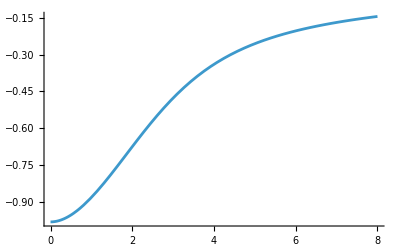

```mathematica
Plot[PhiMetric[r], {r, 0, RStar}]
```

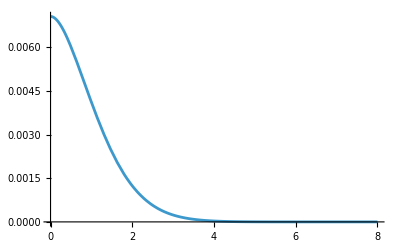

```mathematica
Plot[Pressure[r], {r, 0, RStar}]
```

#### Solving for the new r̄(r) and r(r̄) inside, obtaining r(r̄) via the interpolation trick Sarp explained

```mathematica
(*Defining the ODE*)
drbardr[rbar_, r_] := rbar/r(1 - (2MassFuncInside[r])/r)^(-1/2)
```

Numerically Integrating the above equation.

```mathematica
eq = rbarofr'[r] == drbardr[rbarofr[r], r];
BC = {rbarofr[RStar] == rbarStar};
```

```mathematica
sol2 = NDSolve[
{eq,
BC},
{rbarofr},
{r, rmin, RStar},
WorkingPrecision-> 30
][[1]];
```

```mathematica
rbarofrInside[r_ /; r <= RStar] = rbarofr[r] /. sol2;
```

```mathematica
rbarofrInside[RStar] //N
rbarofrOutside[RStar] //N
```

6.9641

6.9641

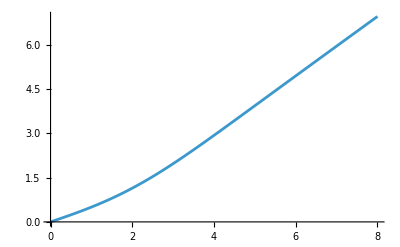

```mathematica
Plot[rbarofrInside[r], {r, 0, RStar}]
```

Now using the interpolation trick to obtain r(r̄):

```mathematica
(*Generating the numerical data points:*)
(*Table[ expression, {variable, start, end, step}*)
data = Prepend[Table[
{rbarofrInside[r], r}, (*Here Mathematica stores rbar[r] and r as a 2 element list - first entry is the independent variable and the one after is the dependent variable*)
{r, rmin, RStar, (RStar - rmin)/10000} (*500 points*)
], {0,0}];
```

```mathematica
(*Evaluates ok at zero as sapr mentioned but integral doesn't like it one bit*)
```

```mathematica
(*Inverse Interpolation*)
rofrbarInside = Interpolation[data];(*Builds a function from the data passing through all points unlike Fit which approximately matches the data to a function I give it with parameters,  FindFit finds the parameters for me given I guess a suitable function*)
```

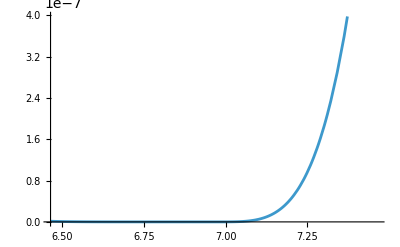

```mathematica
Plot[{Abs[rofrbarInside[rbar]-rofrbarOutside[rbar]]}, {rbar, rbarStar-0.5, rbarStar+0.5}]
```

```mathematica
rofrbarInside[0]
```

0.

#### Writing clean full r(r̄) equation to try and rid discontinuities

```mathematica
rofrbarFull[rbar_?NumericQ] := Piecewise[
{
{rofrbarInside[rbar], rbar < rbarStar},
{rofrbarOutside[rbar], rbar >= rbarStar}
}
];
```

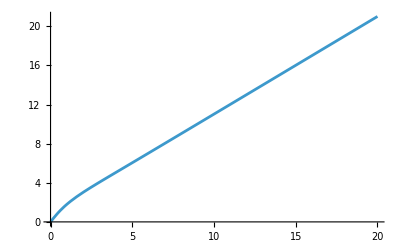

```mathematica
Plot[rofrbarFull[rbar], {rbar, 0, 20}]
```

### Putting this together to find the new interior metric functions

#### finding alpha in terms of normal r first

```mathematica
dPhidrMetric[r_] := ((MassFuncInside[r] + 4 Pi Pressure[r] r^3)/(r(r-2MassFuncInside[r])))
```

```mathematica
alpha[r_] := Exp[PhiMetric[r]]
DERalphaIns[r_] := dPhidrMetric[r] alpha[r]
```

Exterior alpha derivative

```mathematica
DERαOutsiderbardummy = Derivative[1][α][rbar];
DERαOutsiderbar[r_] := ((1-1/(2 rbar))/(2 (1+1/(2 rbar))^2 rbar^2)+1/(2 (1+1/(2 rbar)) rbar^2) )/. rbar -> rbarofrOutside[r] (*More accurate subbing in after for rbar maybe?*)
drbardrOutside[r_] := rbarofrOutside[r]/r(1 - (2M)/r)^(-1/2)
```

```mathematica
DERalpha[r_?NumericQ] := drbardrOutside[r]  DERαOutsiderbar[r]
```

```mathematica
DERalpha[RStar] //N
DERalphaIns[RStar]
```

0.0180422

0.0180421959121758051409108993907

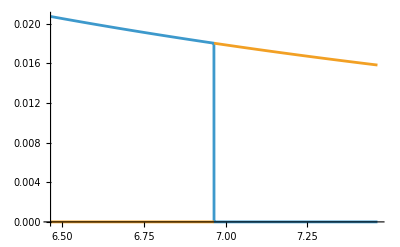

```mathematica
Plot[{Piecewise[{{DERalphaIns[rofrbarInside[rbar]],rbar<=rbarStar}}],Piecewise[{{DERalpha[rofrbarOutside[rbar]],rbar>=rbarStar}}]},{rbar,rbarStar-0.5,rbarStar+0.5}]
```

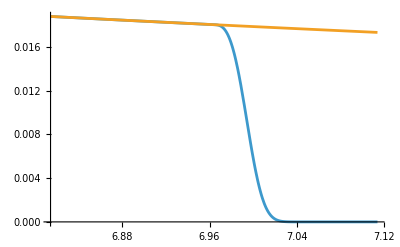

```mathematica
Plot[{DERalphaIns[rofrbarInside[rbar]],DERalpha[rofrbarOutside[rbar]]},{rbar,rbarStar-0.15,rbarStar+0.15}]
```

```mathematica
DERαOutside[rbar_] := drbardrOutside[rofrbarOutside[rbar]]  DERαOutsiderbar[rofrbarOutside[rbar]]
DERαInside[rbar_] := dPhidrMetric[rofrbarInside[rbar]] alpha[rofrbarInside[rbar]]
```

```mathematica
DERαFull[rbar_] := Piecewise[
{
{DERαInside[rbar], rbar < rbarStar},
{DERαOutside[rbar], rbar >= rbarStar}
}
]
```

```mathematica
(*DERαFull[rbar_]:=If[rbar<rbarStar,DERαInside[rbar],DERαOutside[rbar]]*)
```

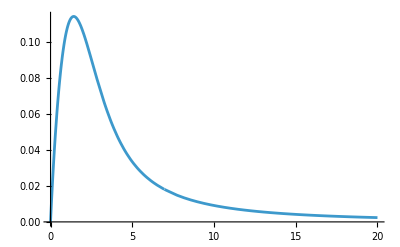

```mathematica
Plot[DERαFull[rbar], {rbar, 0, 20}]
```

```mathematica
αInside[rbar_?NumericQ] := Exp[PhiMetric[rofrbarInside[rbar]]]
```

```mathematica
αInside[rbarStar]
α[rbarStar]
```

0.866025403784438646763723170753

(1-1/(7+4 √3))/(1+1/(7+4 √3))

```mathematica
αFull[rbar_] := Piecewise[
{
{αInside[rbar], rbar < rbarStar},
{α[rbar], rbar >= rbarStar}
}
]
(*αFull[rbar_]:=If[rbar<rbarStar,αInside[rbar],α[rbar]]*)
```

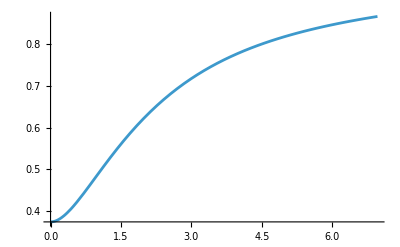

```mathematica
Plot[αFull[rbar], {rbar, 0, rbarStar}]
```

```mathematica
(*Plot[Derivative[1][αFull][rbar], {rbar, 0.4, rbarStar}]*) (*Phi metric causing the issue as it's the numerically integrating thing we are differentiating*)
```

Going to do the same derivative setup as the α component for the A component

```mathematica
AInside[rbar_?NumericQ] := rofrbarFull[rbar]/rbar;
```

```mathematica
A[rbarStar]
AInside[rbarStar]
```

(1+1/(7+4 √3))^2

(1+1/(7+4 √3))^2

```mathematica
AFull[rbar_] := Piecewise[
{
{A[rbar], rbar >= rbarStar},
{AInside[rbar], rbar < rbarStar}
}
];
(*AFull[rbar_]:=If[rbar<rbarStar,AInside[rbar],A[rbar]]*)
```

```mathematica
drbardr[rbar_, r_] := rbar/r(1 - (2MassFuncInside[r])/r)^(-1/2)
drdrbar[rbar_] := rofrbarInside[rbar]/rbar(1 - (2MassFuncInside[rofrbarInside[rbar]])/rofrbarInside[rbar])^(1/2)
```

```mathematica
DERAInside[rbar_] := drdrbar[rbar]/rbar - rofrbarInside[rbar]/rbar^2;
DERAOutside[rbar_] := Derivative[1][A][rbar]
```

```mathematica
DERAFull[rbar_] := Piecewise[
{
{DERAOutside[rbar], rbar >=rbarStar},
{DERAInside[rbar], rbar < rbarStar}
}
];
(*DERAFull[rbar_]:=If[rbar<rbarStar,DERAInside[rbar],DERAOutside[rbar]]*)
```

```mathematica
DERAOutside[rbarStar]
DERAInside[rbarStar]
```

-(4 (1+1/(7+4 √3)))/(7+4 √3)^2

-0.022099489674330444219434

#### Density and Pressure in isotropic coordinates

```mathematica
rho0 = rhoCentre[RStar];
```

```mathematica
rho[rbar_?NumericQ] :=Piecewise[
{
{rho0(1 - rofrbarInside[rbar]/RStar)^6, rbar < rbarStar},
{0, rbar >= rbarStar}
}
];

IsotropicCoordsPressure[rbar_?NumericQ] := Piecewise[
{
{Pressure[rofrbarInside[rbar]], rbar < rbarStar},
{0, rbar >= rbarStar}
}
];
```

```mathematica
rho[rbar_?NumericQ] := rho0(1 - rofrbarInside[rbar]/RStar)^6
```

```mathematica
IsotropicCoordsPressure[rbar_?NumericQ] := Pressure[rofrbarInside[rbar]]
```

```mathematica
Precision[AInside[rbarStar]]
Precision[A[rbarStar]]
Precision[rho0]
```

∞

∞

∞

## Setting up 2D ODEs for new density profile:

### Outside Star

#### Velocities

```mathematica
Ut[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := (√(1 + (ur/A[rbar])^2 + (uphi/(rbar A[rbar]))^2))/α[rbar];
```

#### Rates of change of velocities

```mathematica
drBardt[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := 1/(A[rbar]^2 Ut[rbar, ur, uphi])ur;

dphidtOutside[rbar_?NumericQ,ur_?NumericQ, uphi_?NumericQ] := 1/(rbar^2*A[rbar]^2*Ut[rbar, ur,uphi])uphi;

durdt2DOutside[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := -α[rbar] Ut[rbar, ur, uphi] DERαOutside[rbar] + ur^2/Ut[rbar, ur, uphi](DERAOutside[rbar]/A[rbar]^3) + uphi^2/Ut[rbar, ur, uphi](1/(rbar^3 *A[rbar]^2) + DERAOutside[rbar]/(rbar^2*A[rbar]^3));
```

### Inside Star

#### Velocities

```mathematica
UtInside[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := (√(1 + (ur/AInside[rbar])^2 + (uphi/(rbar AInside[rbar]))^2))/αInside[rbar];
```

#### Rates of change of velocities

```mathematica
drBardtInside[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := 1/(AInside[rbar]^2 UtInside[rbar, ur, uphi])ur;

dphidtInside[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := 1/(rbar^2 AInside[rbar]^2 UtInside[rbar, ur, uphi])uphi;

duphidtInside[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := 0;

durdt2DInside[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := -αInside[rbar] UtInside[rbar, ur, uphi] DERαInside[rbar] + ur^2/UtInside[rbar, ur, uphi](DERAInside[rbar]/AInside[rbar]^3) + uphi^2/UtInside[rbar, ur, uphi](1/(rbar^3 AInside[rbar]^2) + DERAInside[rbar]/(rbar^2 AInside[rbar]^3));
```

## Defining Energy and Angular momentum per unit mass functions along with other orbital parameters

```mathematica
EnergyPerUnitMass[ptilde_?NumericQ, eccen_?NumericQ] := √(((ptilde -2)^2 - 4 *eccen^2)/(ptilde*(ptilde - 3 - eccen^2)));
LPerUnitMass[ptilde_?NumericQ, M_?NumericQ, eccen_?NumericQ] := (ptilde*M)/(√(ptilde - 3 - eccen^2));
ptildefunc[p_?NumericQ, Mass_?NumericQ] := p/Mass;
rapoapsis[eccen_?NumericQ, ptilde_?NumericQ, Mass_?NumericQ] := ((ptilde)*Mass)/(1 - eccen); (*In Schwarzschild areal r coordinates*)
rperiapsis[eccen_?NumericQ, ptilde_?NumericQ] := ptilde/(1+eccen);
```

### Defining the constants to define the motion

#### Eccentricity and semi-latus rectum

```mathematica
eccentricity = 0.4;
semilatrecP = 10;
ptilde = ptildefunc[semilatrecP, M];
```

#### Energy and Angular momentum per unit mass

```mathematica
Energy = EnergyPerUnitMass[ptilde, eccentricity];
AngularMomentumUphi0 = LPerUnitMass[ptilde, M, eccentricity];
```

Initial drop radius (apoapsis), closest point it goes to (perihelion), defining Isotropic star radius

```mathematica
r0 = rapoapsis[eccentricity, ptilde, M];
rbar0 = rbarofrOutside[r0];
```

#### Must satisfy this inequality to pass through star

```mathematica
ptilde < RStar(1+eccentricity)
ptilde > 6 + 2eccentricity
```

True

True

## Solving the ODEs

```mathematica
drBardtInside[rbarStar,0, AngularMomentumUphi0]
durdt2DInside[rbarStar,0, AngularMomentumUphi0]
duphidtInside[rbarStar,0, AngularMomentumUphi0]
dphidtInside[rbarStar,0, AngularMomentumUphi0]
```

0.

0.00219943

0

0.0466817

```mathematica
t0=0;
tEnd=10000;

solIn=NDSolve[
{
rbar'[t]==
Piecewise[
{
{drBardt[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{drBardtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
ur'[t]==
Piecewise[
{
{durdt2DOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{durdt2DInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
uphi'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{duphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
phi'[t]==
Piecewise[
{
{dphidtOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{dphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
rbar[t0]== rbar0,
ur[t0]==0,
phi[t0]==0,
uphi[t0]==AngularMomentumUphi0,

WhenEvent[rbar[t] <= 10^-2 , "StopIntegration"]
},
{rbar,ur,phi,uphi},
{t,t0,tEnd},
MaxSteps->Infinity,
WorkingPrecision->30
][[1]];
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (30.).

InterpolatingFunction::dmval: Input value {6.96465721842042805636296324889} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.000552739500596988815818791} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
massNumIn = mass /. solIn;
```

```mathematica
tFinish = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}]
```

10000.

159.895

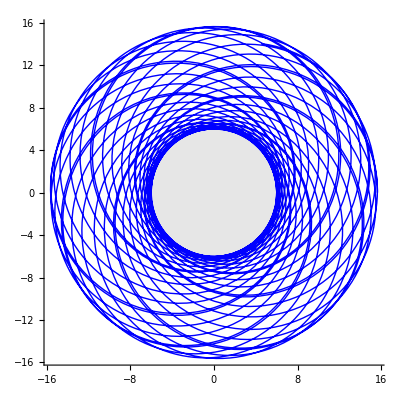

```mathematica
x[t_]:=rbarNumIn[t] Cos[phiNumIn[t]];
y[t_]:=rbarNumIn[t] Sin[phiNumIn[t]];
orbit2D=ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio->Automatic,AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Thick,Blue}];
(*Automatic scale makes the aces the same scale*)
centralBody=Graphics[{GrayLevel[0.9],Disk[{0,0},rbarStar]}];
Show[centralBody, orbit2D,AspectRatio->Automatic,PlotRange->All, Axes -> True]
```

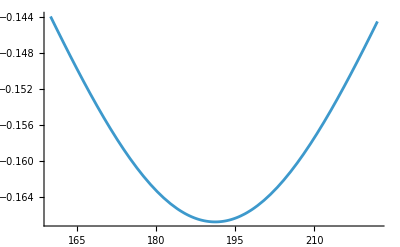

```mathematica
Plot[PhiMetric[rofrbarInside[rbarNumIn[t]]], {t, 160, 222}]
```

```mathematica
Plot[PhiMetric[r], {r, 0, RStar}]
```

-Graphics-

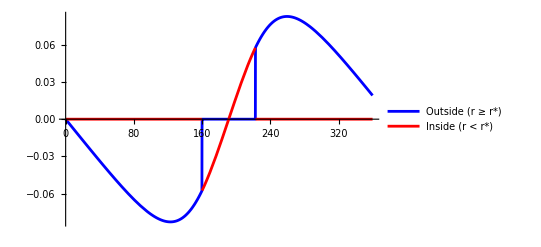

```mathematica
Plot[{Piecewise[{{drBardt[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]>=rbarStar}}],Piecewise[{{drBardtInside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}}]},{t,0,tSurface+200},PlotStyle->{Blue,Red},PlotLegends->{"Outside (r ≥ r*)","Inside (r < r*)"}]
```

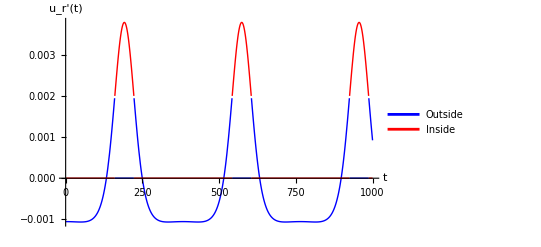

```mathematica
Plot[{Piecewise[{{durdt2DOutside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]>=rbarStar}}],Piecewise[{{durdt2DInside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}}]},{t,0,tFinish},PlotRange->All,PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick]},PlotLegends->{"Outside","Inside"},AxesLabel->{"t","u_r'(t)"}]
```

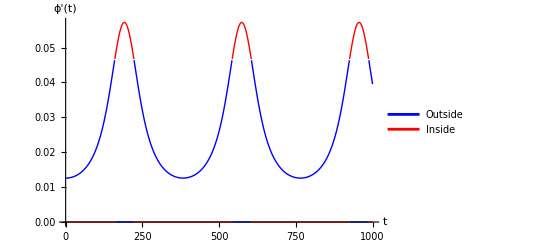

```mathematica
Plot[{Piecewise[{{dphidtOutside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]>=rbarStar}}],Piecewise[{{dphidtInside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}}]},{t,0,tFinish},PlotRange->All,PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick]},PlotLegends->{"Outside","Inside"},AxesLabel->{"t","ϕ'(t)"}]
```

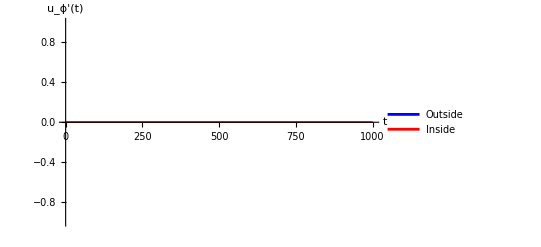

```mathematica
Plot[{Piecewise[{{0,rbarNumIn[t]>=rbarStar}}],Piecewise[{{duphidtInside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}}]},{t,0,tFinish},PlotRange->All,PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick]},PlotLegends->{"Outside","Inside"},AxesLabel->{"t","u_ϕ'(t)"}]
```

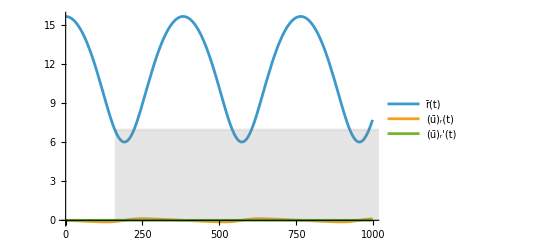

```mathematica
outFigRadial=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

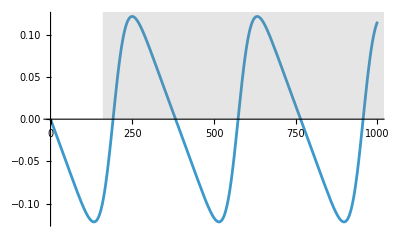

```mathematica
outFigRadial=Show[Plot[{urNumIn[t]},{t,t0, tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

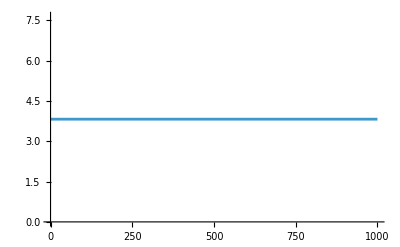

```mathematica
outFigAngular=Plot[{uphiNumIn[t]},{t,t0,tFinish},PlotLegends->LineLegend[Automatic,{"phi(t)","uphi(t)","uphi'(t)"}]]
```